#### Test :: vertices from MorphologicalGraph is same as MorphologicalBranchPoints

```mathematica
testimg={-Graphics-,Thinning@-Graphics-};
```

```mathematica
img=testimg[[-1]];
```

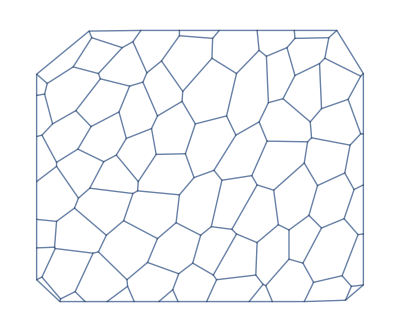

```mathematica
graph=Graph[MorphologicalGraph[img],ImageSize->Tiny]
```

```mathematica
SetAttributes[findvert,HoldFirst];
findvert[graph_Graph]:=With[{g=Unevaluated[graph]},
First@Cases[g,HoldPattern[VertexCoordinates->x_]:> x,{2}]
]
```

```mathematica
(Sort@ImageValuePositions[MorphologicalBranchPoints[img],1]==Sort[findvert[-Graphics-]])
```

True

## Force Inference: M3

### image operations

```mathematica
ClearAll@segmentImage;
segmentImage[binarizedMask_?ImageQ,border: True|False]:=
Which[!border,
Print["border not present, segmenting with morphological components"];
ArrayComponents@DeleteBorderComponents@MorphologicalComponents[ColorNegate@binarizedMask, CornerNeighbors->False],
border,
Print["border exists, segmenting with watershed components"];
WatershedComponents[binarizedMask, CornerNeighbors->False]
];
```

```mathematica
Clear@bresenhamLine;
bresenhamLine[p0_,p1_]:=Module[{dx,dy,sx,sy,err,newp},
{dx,dy}=Abs[p1-p0];
{sx,sy}=Sign[p1-p0];
err=dx-dy;
newp[{x_,y_}]:=With[{e2=2 err},{If[e2>-dy,err-=dy;x+sx,x],If[e2<dx,err+=dx;y+sy,y]}];
NestWhileList[newp,p0,#=!=p1&,1]
];
```

```mathematica
ClearAll@closeImage;
closeImage[image_]:=Module[{morphImage, morphImagePos,posConv,ptsOrdered},
morphImage=MorphologicalTransform[image,"SkeletonEndPoints"];
morphImagePos=PixelValuePositions[morphImage,1];
posConv=With[{mean=Mean@N@morphImagePos},
ptsOrdered=Append[#,First@#]&[SortBy[morphImagePos,ArcTan@@(mean-#)&]];
DeleteDuplicates@Flatten[bresenhamLine@@@Partition[ptsOrdered,2,1,1],1]
];
ReplacePixelValue[image,posConv-> 1]
];
```

```mathematica
If[Length@Kernels[]==0,LaunchKernels[]]
ClearAll@getImageAttributes;
getImageAttributes[img_,padded_:False,closed_:False]:=Module[{image=img,segmentation,masks,branchpts,vertgroupings,
cellToVertices,cellvertgroupings},
If[!closed,image=closeImage[image]];
segmentation=If[!padded,
segmentImage[image,closed],
MorphologicalComponents[ColorNegate@image,CornerNeighbors->False]//DeleteBorderComponents
];
Echo@Image[Colorize@segmentation,ImageSize->Medium];
masks=Values@ComponentMeasurements[segmentation,"Mask"];
branchpts=MorphologicalBranchPoints@image;
vertgroupings=ParallelTable[ImageValuePositions[(Dilation[Image@masks[[i]],1]*branchpts),1],{i,Length[masks]}];
cellvertgroupings=Association@MapIndexed[First@#2->#1&,vertgroupings];
cellvertgroupings=Normal@GroupBy[Flatten[Thread/@Normal@cellvertgroupings,1],Last->First];
cellvertgroupings=(v↦Map[#->First[v]&,Last[v]])/@DeleteCases[cellvertgroupings,HoldPattern[_->{_Integer}]]//GroupBy[First->Last]@*Flatten;
cellvertgroupings=Block[{mean},
(mean=Mean@#;
Function[x,SortBy[x,ArcTan@@(#-mean)&,Greater]][#])&/@cellvertgroupings
];
{segmentation,MorphologicalGraph@image,cellvertgroupings}
];
```

{KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…]}

### forming network topology

```mathematica
ClearAll@getGraphAttributes;
SetAttributes[getGraphAttributes,HoldFirst];
getGraphAttributes[graph_,image_]:=Block[{vertexCoords,vList,edgeList,ptsToIndAssoc,indToPtsAssoc,vertexToEdge,pts,diff,rules},
Clear@borderAdjust;
With[{dim=First@ImageDimensions@image},
borderAdjust[x_/;x==1.5]:=x-1;
borderAdjust[x_/;x==dim-1.5]:=x+1;
borderAdjust[x_]:=x;
];

vertexCoords=With[{g=Unevaluated@graph},
First@Cases[g,HoldPattern[VertexCoordinates->x_]:>x,{2}]
];
vList=VertexList[graph];
vertexCoords=Thread@MapAt[borderAdjust,Transpose@vertexCoords,{1,All}];
ptsToIndAssoc=AssociationThread[vertexCoords->vList];
diff=Sort[vertexCoords]-Sort[ImageValuePositions[MorphologicalTransform[image,{"SkeletonBranchPoints"}],1]];
rules=Thread[
Sort[vertexCoords]->(Sort[vertexCoords]+(Which[#=={0.,0.},#,
#=={1.,0.},{-1.,0.},
#=={-1.,0.},{1.,0.},
#=={0.,1.},{0.,-1.},
#=={0.,-1.},{0.,1.}]&/@diff))
];
$rules=rules;
indToPtsAssoc=AssociationThread[
(ptsToIndAssoc[#]&/@Sort[vertexCoords])->
(Sort[vertexCoords]+(Which[#=={0.,0.},#,
#=={1.,0.},{-1.,0.},
#=={-1.,0.},{1.,0.},
#=={0.,1.},{0.,-1.},
#=={0.,-1.},{0.,1.}]&/@diff))
];
ptsToIndAssoc=AssociationMap[Reverse,indToPtsAssoc];
edgeList=(#~Join~Reverse[#,2])&@EdgeList[graph]/.UndirectedEdge->List;
vertexToEdge=GroupBy[edgeList,First]; (*vertex -> edges it is a part of*)
{ptsToIndAssoc,indToPtsAssoc,vertexToEdge}
];
```

```mathematica
ClearAll@formTopology;
formTopology[ptsToIndAssoc_,indToPtsAssoc_,vertexToEdge_,cellToVertices_]:=Block[{cellVertexGrouping,edges,
smalledge,prevVertexCoords,newVertices,maxVertexInd,newind,PtoIAssoc=ptsToIndAssoc,newaddition,
ItoPAssoc=indToPtsAssoc,VtoE=vertexToEdge,CtoV=cellToVertices,smalledgepos,delVertices,VtoC,
unorderedKeys,orderedkeys,replacerules},
edges=Flatten[Values@VtoE,1];
(*FixedPoint[(smalledgepos=FirstPosition[Map[EuclideanDistance@@Lookup[ItoPAssoc,#]&,#],x_/;x<3];
If[smalledgepos≠{},
smalledge=Extract[edges,smalledgepos];
delVertices=Flatten@smalledge;
prevVertexCoords=Lookup[ItoPAssoc,delVertices];
newVertices=Mean[Lookup[ItoPAssoc,#]&/@smalledge];
maxVertexInd=Max[Keys@ItoPAssoc];
newind=maxVertexInd+1;
newaddition=newind-> newVertices;
KeyDropFrom[ItoPAssoc,delVertices];
AssociateTo[ItoPAssoc,newaddition]; (*delete prev vertex and add new*)
KeyDropFrom[PtoIAssoc,prevVertexCoords];
AssociateTo[PtoIAssoc,Reverse@newaddition]; (*deletion and addition*)
CtoV=DeleteDuplicates/@Replace[CtoV,Dispatch@Thread[delVertices->newind],{2}];
edges=DeleteCases[edges,delVertices|Reverse@delVertices];(*delete from edges*)
edges=edges/.Thread[delVertices->newind],
None];
edges)&,edges];*)
unorderedKeys=Keys@ItoPAssoc;
orderedkeys=Range[Length@unorderedKeys];
replacerules=Dispatch@Thread[unorderedKeys->Range[Length@unorderedKeys]];
edges=edges/.replacerules;
ItoPAssoc=AssociationThread[orderedkeys->Values@ItoPAssoc];
PtoIAssoc = AssociationMap[Reverse,ItoPAssoc];
VtoE=KeySort@GroupBy[edges,First];
CtoV=CtoV/.replacerules;
VtoC=KeySort@GroupBy[Reverse[Flatten[Thread/@Normal@CtoV,1],2],First->Last];
{PtoIAssoc,ItoPAssoc,VtoE,CtoV,VtoC}
];
```

### force inference

```mathematica
Clear@formAndComputeMatrices;
formAndComputeMatrices[vertexCoordinatelookup_,inds_,colsOrder_,edgenum_,delV_,vertexToCells_,vertexvertexConn_,maxcellLabels_,filteredvertices_,vertexAssoc_]:=Module[{tx,ty,tensinds,filteredvertexnum,relabelvert,spArrayTx,spArrayTy,spArrayPx,spArrayPy,spArrayX,spArrayY,$filteredvertices},
{tx,ty}=Transpose[
With[{target=vertexCoordinatelookup[#[[2]]],source=vertexCoordinatelookup[#[[1]]]},
(target-source)/Norm[target-source]
]&/@inds];
Print["Tension coefficients computed: ",Style["☑",20]];MapThread[Print[Style["counts of zero coefficients "<>#1,Red],Count[#2,0.]]&,{{"Tx: ","Ty: "},{tx,ty}}];$filteredvertices=Complement[filteredvertices,delV];filteredvertexnum=Length@$filteredvertices;relabelvert=AssociationThread[$filteredvertices-> Range[Length@$filteredvertices]];tensinds=Thread[{Lookup[relabelvert,Part[inds,All,1]],colsOrder}];spArrayTx=spArrayTy=SparseArray@ConstantArray[0,{filteredvertexnum,edgenum}];MapThread[(spArrayTx[[Sequence@@#1]]=#2)&,{tensinds,tx}];MapThread[(spArrayTy[[Sequence@@#1]]=#2)&,{tensinds,ty}];spArrayPx=spArrayPy=SparseArray@ConstantArray[0,{filteredvertexnum,maxcellLabels}];MapThread[Print[Style[#1<> "coefficients stats: ",Blue],Counts@Map[Total@*Unitize,Normal[#2]]]&,{{"Tx ", "Ty "},{spArrayTx,spArrayTy}}];Print[Style["Tension coefficients dist: ",Bold],Histogram[{{},Join[spArrayTx["NonzeroValues"],spArrayTy["NonzeroValues"]]},20,ImageSize->Small]];
Block[{neighbouringCells,bisectionlabels,bisectpts,centroid,orderingT,vertexcoords,orderptsT,orderIndT,orderCells,kk=0,px,py},
With[{cellToVertexLabelsT= Reverse[vertexToCells,2],
edgeVertexPart=GroupBy[vertexvertexConn~Flatten~1 ,First->Last]},
With[{cellToAllVerticesT= GroupBy[Flatten[Thread/@cellToVertexLabelsT],First->Last]},
Do[
neighbouringCells= vertexToCells[[i,2]]; (* for vertex, the neighbouring cell labels *)bisectionlabels=Intersection[cellToAllVerticesT[#],edgeVertexPart[i]]&/@neighbouringCells ;If[Length[neighbouringCells]>2 && MatchQ[bisectionlabels,{Repeated[{_,_},{3,∞}]}],(vertexcoords=DeleteDuplicates[vertexCoordinatelookup[#]&/@Flatten@bisectionlabels];centroid=Mean@vertexcoords;orderingT=Ordering[ArcTan[Last@#-Last@centroid,First@#-First@centroid]&/@vertexcoords];orderptsT=vertexcoords[[orderingT]];orderIndT=Partition[Lookup[vertexAssoc,Append[orderptsT,First@orderptsT]],2,1];
orderCells =Last@@@Position[(x↦ Map[Intersection[x,#]&,orderIndT])/@(cellToAllVerticesT[#]&/@neighbouringCells),x_/;Length[x]==2];neighbouringCells=neighbouringCells[[orderCells]];bisectpts=Map[vertexCoordinatelookup,orderIndT,{2}];{px,py}=Transpose[{(#[[2,2]]-#[[1,2]])/2,-(#[[2,1]]-#[[1,1]])/2}&/@bisectpts];If[MemberQ[px,0.]||MemberQ[py,0.],kk++];{px,py})
];
Scan[(spArrayPx[[ Sequence@@#[[1]] ]]=#[[2]])&,Thread[Thread[{relabelvert@i,neighbouringCells}]-> px]];Scan[(spArrayPy[[ Sequence@@#[[1]] ]]=#[[2]])&,Thread[Thread[{relabelvert@i,neighbouringCells}]-> py]],{i,$filteredvertices}]
]
];
Print["Pressure coefficients computed: ",Style["☑",20]];
Print[Style["Pressure coefficients zero: ",Red],kk ];
];
MapThread[Print[Style[#1<> "coefficients stats: ",Blue],Counts@Map[Total@*Unitize,Normal[#2]]]&,
{{"Px ", "Py "},{spArrayPx,spArrayPy}}];
Print[Style["pressure coefficients dist: ",Bold],
Histogram[{{},Join[spArrayPx["NonzeroValues"],spArrayPy["NonzeroValues"]]},ImageSize->Small]];spArrayX=Join[spArrayTx,spArrayPx,2];spArrayY=Join[spArrayTy,spArrayPy,2];{spArrayX,spArrayY,Dimensions[spArrayTx],Dimensions[spArrayPx]}
];
```

```mathematica
(* maximize Log-likelihood function *)
ClearAll@maximizeLogLikelihood;
maximizeLogLikelihood[spArrayX_,spArrayY_,dimTx_,dimPx_]:= Module[{range=10.0^Range[-1.5,1.5,0.1],sol,spA,spg,spB,n,m,spb,τ,SMatrix,Q,R,H,h,logL,μ,p},Print[Style["\nmaximum likelihood estimator",Bold,18]];sol=With[{ls=range},
(*spA=SparseArray@(Join[spArrayX,spArrayY]);*)
spA=SparseArray@(Flatten[Transpose[{spArrayX,spArrayY}],1]);spg=SparseArray@(ConstantArray[1.,Last@dimTx]~Join~ConstantArray[0.,Last@dimPx]);spB=SparseArray@DiagonalMatrix[spg];n=First@Dimensions@spA;m=(Length[#]-Total@#)&@Diagonal[spBᵀ.spB];With[{DimspB=First[Dimensions@spB]},
spb=SparseArray@ConstantArray[0.,First[Dimensions@spA]];
Table[(τ=Sqrt[μ];SMatrix=SparseArray@(Map[Flatten]@Transpose[{Join[spA,τ spB],Join[spb,τ spg]},{2,1}]);{Q,R}=SparseArray/@QRDecomposition[SMatrix];R=DiagonalMatrix[Sign[Diagonal@R]].R;H=R[[;;#,;;#]]&@DimspB;h⃗=R[[;;#,#+1]]&@DimspB;h=R[[#+1,#+1]]&@DimspB;logL=-(n-m+1)*Log[h^2]+Total[Log[Diagonal[μ (spBᵀ.spB)]["NonzeroValues"]]]-2*Total[Log[Diagonal[H[[1;;-2,1;;-2]]]["NonzeroValues"]]]),{μ,ls}]
]
];Print[ListPlot[{sol,sol},Joined->{True,False},PlotStyle->{{Red,Thick},{PointSize[0.02],Black}},AxesStyle->{{Black},{Black}},AxesLabel->{"index μ","LogLikelihood"},Background->LightBlue,
PlotRange->All]];μ=Keys@@MaximalBy[Thread[range->sol],Values,1];Print["optimized value of μ: ",μ];τ=Sqrt[μ];With[{DimspB=First[Dimensions@spB]},
SMatrix=SparseArray@(Map[Flatten]@Transpose[{Join[spA,τ spB],Join[spb,τ spg]},{2,1}]);{Q,R}=SparseArray/@QRDecomposition[SMatrix];R=DiagonalMatrix[Sign[Diagonal@R]].R;H=R[[;;#,;;#]]&@DimspB;h⃗=R[[;;#,#+1]]&@DimspB;
];
p=PseudoInverse[H].h⃗; p
];
```

```mathematica
coolmap[t_?NumericQ]:=Blend[{RGBColor[{Rational[33, 85], Rational[67, 85], Rational[71, 85]}],RGBColor[{Rational[161, 255], Rational[89, 255], Rational[163, 255]}]},t]/;0≤t≤1;

ClearAll@plotTPMaps;
plotTPMaps[p_,segmentation_,segmentationB_,edgeImg_,maxcellLabels_,dimTx_,vertexToCells_,vertexCoordinatelookup_,edgeLabels_,paddedQ_]:=Module[{cellToVertexLabels,cellToAllVertices,ptsEdges,k,v,ord,edgeptAssoc,poly,pts,outer,mean,ordering,orderpts,tvals,cols,pvals,removecollabels,collabels,pressurecolours,tbar,pbar},
cellToVertexLabels= Reverse[vertexToCells,2];
cellToAllVertices= GroupBy[Flatten[Thread/@cellToVertexLabels],First->Last];
(* polygons *)
ptsEdges ={{1,1},Reverse@Dimensions[segmentation],{Last[Dimensions@segmentation],1},{1,First[Dimensions@segmentation]}};{k,v}={Keys@#,Values[#][[All,2]]}&@ComponentMeasurements[segmentation,{"AdjacentBorderCount","Centroid"},#==2&];ord=Flatten[Function[x,Position[#,Min[#]]&@Map[EuclideanDistance[#,x]&,ptsEdges]]/@v];edgeptAssoc=Association[Rule@@@Thread[{k,ptsEdges[[ord]]}]];
poly=(
pts=vertexCoordinatelookup/@cellToAllVertices[#];If[MemberQ[k,#],AppendTo[pts,edgeptAssoc[#]],pts];mean=Mean[pts];ordering=Ordering[ArcTan[First@#-First@mean,Last@#-Last@mean]&/@pts];orderpts=pts[[ordering]];Polygon@Append[orderpts,First@orderpts]
)&/@Range[maxcellLabels];

tvals=Rescale@p[[1;;Last@dimTx]];
cols=ColorData["Rainbow"][#]&/@tvals;
tbar=BarLegend["Rainbow",SetPrecision[Sort@tvals,2],LegendMarkerSize->150];
Print["Tension map:"];
Print[GraphicsRow[{Graphics[{Thickness[0.005],Riffle[cols,Line/@Values@edgeLabels]}],tbar}]];

pvals=p[[ Last[dimTx]+1;;]];
removecollabels=If[paddedQ,
outer=Keys@@ComponentMeasurements[segmentationB,"AdjacentBorders",Length@#≠ 0&];
removecollabels=Keys@Cases[
ComponentMeasurements[Dilation[segmentationB,1],"Neighbors"],
PatternSequence[_->{___,outer,___}]];
removecollabels-UnitStep[removecollabels-outer],
Keys@ComponentMeasurements[segmentation,"AdjacentBorders",Length[#]>0&]
];
collabels=Complement[Range@maxcellLabels,removecollabels];
(*pressurecolours=ColorData["Rainbow"][#]&/@Rescale[(pvals[[collabels]])];*)
pressurecolours=coolmap/@Rescale[(pvals[[collabels]])];
(*pbar=BarLegend["Rainbow",SetPrecision[Rescale[pvals[[collabels]]],2],LegendMarkerSize->150];*)
pbar=BarLegend[{coolmap/@Sort@Rescale[(pvals[[collabels]])],MinMax@(pvals[[collabels]])}];
Print["Pressure map:"];
Print@GraphicsRow[{Show[Graphics@Riffle[pressurecolours,poly[[collabels]]],edgeImg],pbar}];
{poly[[collabels]],pvals[[collabels]],p[[1;;Last@dimTx]],poly}
];
```

```mathematica
ClearAll@forceInference;
forceInference[img_,cellToVerticesOrig_,indToPtsAssoc_,ptsToIndAssoc_,segmentation_,vertexToEdge_,paddedQ_,scale_:500]:=Block[{ptsToIndAssocC=ptsToIndAssoc,indToPtsAssocC,filteredvertices,vertexvertexConn,delV,inds,edgeLabels,vertToedges,colsOrder,edgenum,maxcellnum,vertexToCellsN,edgeLabelsC,segmentationB,outsidevertices,possibleOuterEdges,spArrayX,spArrayY,dimTx,dimPx,p,edges,edgeImg,cellToVertices,vertexToCells,inneredges,vertexToEdgeC=vertexToEdge,cells,pvals,tvals,edgeAssoc,tensionAssoc,polys},

cellToVertices=Map[Lookup[ptsToIndAssocC,#]&,cellToVerticesOrig];
{ptsToIndAssocC,indToPtsAssocC,vertexToEdgeC,cellToVertices,vertexToCells}=formTopology[ptsToIndAssoc,indToPtsAssoc,vertexToEdge,cellToVertices];
SeedRandom[11];
Print@Grid[{{Graphics[Values@Map[Line@Lookup[indToPtsAssocC,#]&,vertexToEdgeC,{2}],ImageSize->Small],
Graphics[Values@Map[{RandomColor[],Polygon@Lookup[indToPtsAssocC,#]}&,cellToVertices],ImageSize->Small]}}
];
edges=DeleteDuplicatesBy[Flatten[Values@vertexToEdgeC,1],Sort];
outsidevertices=Keys@Select[Length/@vertexToCells,#==2&];
possibleOuterEdges=Flatten[
Map[x↦Cases[edges,p:{PatternSequence[x,_]}:> 
If[Length@Intersection[outsidevertices,p]>1,p,Nothing]
],outsidevertices],1];
inneredges=DeleteCases[edges,Alternatives@@possibleOuterEdges];edgeImg=Graphics[{Thick,Map[Line@Lookup[indToPtsAssocC,#]&,inneredges]},ImageSize->Medium];
Print@edgeImg;
filteredvertices=Keys@Select[vertexToCells,(Length[#]>2&)];
vertexvertexConn= ParallelTable[
Cases[inneredges,{OrderlessPatternSequence[i,p_]}:>{i,p}],
{i,filteredvertices}];
delV=Cases[vertexvertexConn,{{p_,_},{p_,_}}:>p];
vertexvertexConn=DeleteCases[vertexvertexConn,{_,_}];
inds=vertexvertexConn~Flatten~1;
edgeLabels=AssociationThread[Range[Length@inneredges]->inneredges];
vertToedges=Normal@AssociationMap[Reverse,edgeLabels];
colsOrder=Flatten[Cases[vertToedges,PatternSequence[{OrderlessPatternSequence@@#}->p_]:>p,∞]&/@inds];
edgenum=Length@inneredges;
maxcellnum=Length@Keys@ComponentMeasurements[segmentation,"Count"];
vertexToCellsN=Normal@vertexToCells;
edgeLabelsC=Lookup[indToPtsAssocC,#]&/@edgeLabels;
segmentationB=MorphologicalComponents[ColorNegate@img,CornerNeighbors->False];
{spArrayX,spArrayY,dimTx,dimPx} = formAndComputeMatrices[indToPtsAssocC,inds,colsOrder,edgenum,delV,vertexToCellsN,vertexvertexConn,maxcellnum,filteredvertices,ptsToIndAssocC];p = maximizeLogLikelihood[spArrayX,spArrayY,dimTx,dimPx];
{cells,pvals,tvals,polys}=plotTPMaps[p,segmentation,segmentationB,edgeImg,maxcellnum,dimTx,vertexToCellsN,indToPtsAssocC,edgeLabelsC,paddedQ];
edgeAssoc=AssociationMap[Reverse,Map[List@*Apply[OrderlessPatternSequence],edgeLabelsC,{1}]];
tensionAssoc=AssociationThread[Range[Length@tvals]->tvals];
Print["local stress tensor map:"];
localStressTensorMap[cells,edgeAssoc,pvals,tensionAssoc,scale];
$cells=cells;
$edgeAssoc=edgeAssoc;
$pvals=pvals;
$tensionAssoc=tensionAssoc;
];
```

### stress map

```mathematica
Clear@localStressTensorMap;
localStressTensorMap[polys_,edgeAssoc_,pressure_,tensionAssoc_,factor_]:=Block[{cell,A,edges,mat,P,T,r,xx,yy,eigvals,eigvecs,centroid,princStress,edgesOrdless,edgeinds,pts},
princStress=MapIndexed[(cell=#1;P=pressure[[First@#2]];
centroid=RegionCentroid[cell];
If[SimplePolygonQ@cell,
edges=MeshPrimitives[cell,1]/.Line->Sequence;
A=Area[cell],
pts=MeshPrimitives[cell,0]/.Point->Sequence;
edges=Partition[pts,2,1,1];
A=Polygon@pts//Area;
];
edgesOrdless=Replace[edges,List->List@*OrderlessPatternSequence,{2},Heads->True];
edgeinds=edgeAssoc/@edgesOrdless;
T=Lookup[tensionAssoc,edgeinds];
mat=(-P A({{1, 0}, {0, 1}})+∑_(i=1)^(Length@edges) (With[{L=edges[[i]]},{Subscript[r, xx],Subscript[r, yy]}=Subtract@@Reverse@L;T[[i]]/Norm[L]({{Subscript[r, xx] Subscript[r, xx], Subscript[r, xx] Subscript[r, yy]}, {Subscript[r, yy] Subscript[r, xx], Subscript[r, yy] Subscript[r, yy]}})]))/A;
{eigvals,eigvecs}=Eigensystem[mat];
MapThread[Line[{centroid-#1#2,#1 #2+centroid}]&,{factor eigvals,eigvecs}])&,polys];Print@Graphics[{{EdgeForm[Black],FaceForm[LightBlue],polys},{Red,princStress}}];
];
```

```mathematica
Clear@createGrid;
createGrid[image_,nx_,ny_]:=Block[{nX,nY,imgdim=ImageDimensions@image,rects},
{nX,nY}={Floor[First[imgdim]/nx],Floor[Last[imgdim]/ny]};
rects=Flatten@Table[Rectangle[{i*nX,j*nY},{(i+1)*nX,(j+1)*nY}],
{i,0,nx-1},{j,0,ny-1}];
Echo@Show[image,Graphics[{Red,EdgeForm[Orange],FaceForm[None],rects}]];
rects
];
```

```mathematica
Clear@globalStressTensorMap;
globalStressTensorMap[image_,window_:{2,2},polys_,edgeAssoc_,pvals_,tensionAssoc_,scale_:500]:=Block[{rects,pos,bounds,cellCandidates,posSel,cells,P,A,T,edges,edgeinds,r,xx,yy,mat,eigvals,eigvecs,regcent,princStress},
rects=createGrid[image,Sequence@@window];
princStress=(bounds=#;
(*regcent=RegionCentroid@bounds;*)
pos=Position[RegionDisjoint[bounds,#]&/@polys,False];
cellCandidates=Extract[polys,pos];
posSel=Pick[pos,Thread[(Area@RegionIntersection[#,bounds]&/@cellCandidates)/Area[cellCandidates]≥0.5],True];
cells=Extract[polys,posSel];
regcent=Mean[RegionCentroid/@cells];
(*regcent=RegionCentroid@RegionUnion[cells];*)
(*Print@Graphics[{{EdgeForm[Red],FaceForm[None],bounds},{FaceForm[None],EdgeForm[Black],cells}}];*)
P=Extract[pvals,posSel];
A=Area@cells;
edges=Flatten[MeshPrimitives[#,1]&/@cells]/.Line->Sequence//DeleteDuplicates@*Map[Sort];
edgeinds=edgeAssoc/@Map[List@*Apply[OrderlessPatternSequence],edges,{1}];
T=Lookup[tensionAssoc,edgeinds];
mat=(-∑_(j=1)^(Length@cells) P[[j]] A[[j]]({{1, 0}, {0, 1}})+∑_(i=1)^(Length@edges) (With[{L=edges[[i]]},{Subscript[r, xx],Subscript[r, yy]}=Subtract@@Reverse@L;T[[i]]/(Norm@L)({{Subscript[r, xx] Subscript[r, xx], Subscript[r, xx] Subscript[r, yy]}, {Subscript[r, yy] Subscript[r, xx], Subscript[r, yy] Subscript[r, yy]}})]))/Total[A];
{eigvals,eigvecs}=Eigensystem@mat;
MapThread[Line[{regcent-scale#1 #2,regcent+scale #1 #2}]&,{eigvals,eigvecs}]
)&/@rects;
Graphics[{EdgeForm[Gray],FaceForm[LightBlue],polys,Thick,Blue,princStress,EdgeForm[{Red,Thin,Dashed}],FaceForm[None],rects}]
];
```

## Runs

#### example 1

```mathematica
image=Thinning@Import["D:\\LocalData\\hashmial\\Research\\Scripts\\force inference\\network_final.tif"];
```

-Graphics-

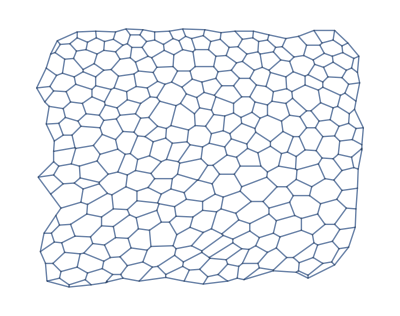

```mathematica
{segmentation,graphimage,cellToVerticesOrig}=getImageAttributes[image,True,True];
Echo@Graph[graphimage,ImageSize-> Tiny];
```

```mathematica
{ptsToIndAssoc,indToPtsAssoc,vertexToEdge}=getGraphAttributes[-Graphics-,Thinning@image];
```

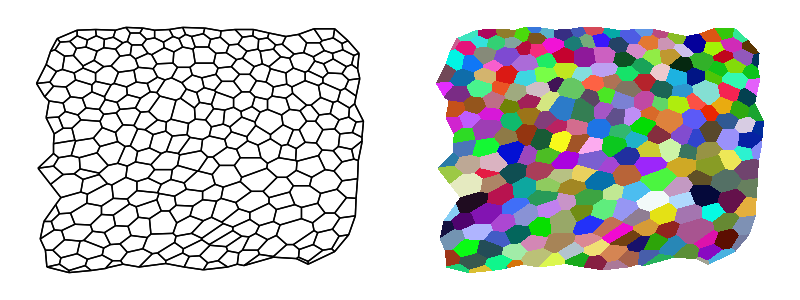

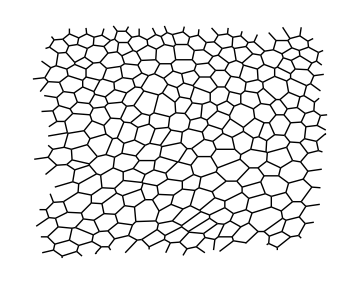

Tension coefficients computed: ☑

counts of zero coefficients Tx: 40

counts of zero coefficients Ty: 54

Tx coefficients stats: <|3→424,2→40|>

Ty coefficients stats: <|3→410,2→54|>

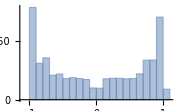
Tension coefficients dist: -Graphics-

Pressure coefficients computed: ☑

Pressure coefficients zero: 33

Px coefficients stats: <|3→441,2→23|>

Py coefficients stats: <|3→453,2→11|>

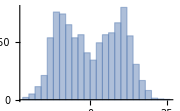
pressure coefficients dist: -Graphics-

maximum likelihood estimator

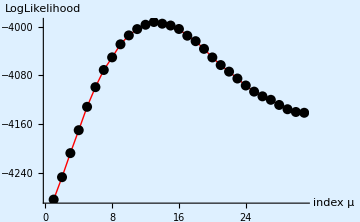

optimized value of μ: 0.501187

Tension map:

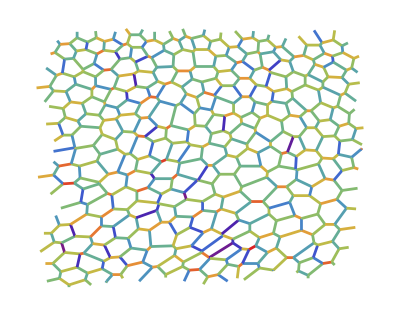

Pressure map:

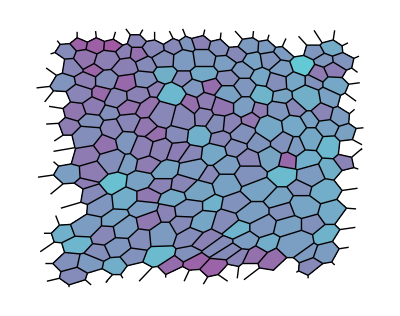

local stress tensor map:

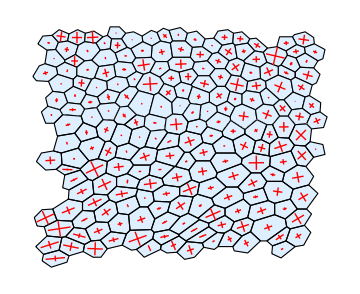

```mathematica
forceInference[image,cellToVerticesOrig,indToPtsAssoc,ptsToIndAssoc,segmentation,vertexToEdge,True]
```

global stress tensor map:

-Graphics-

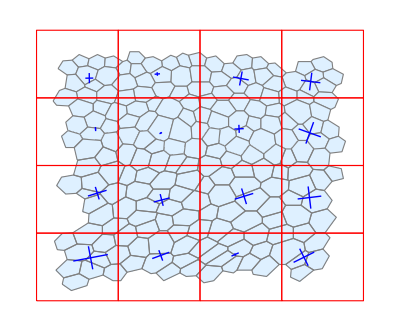

```mathematica
Print["global stress tensor map:"];
globalStressTensorMap[image,{4,4},$cells,$edgeAssoc,$pvals,$tensionAssoc,1500]
```

#### example 2

```mathematica
image=Binarize[Import@"D:\\LocalData\\hashmial\\Data from Clementine\\1.tif"];
```

border exists, segmenting with watershed components

-Graphics-

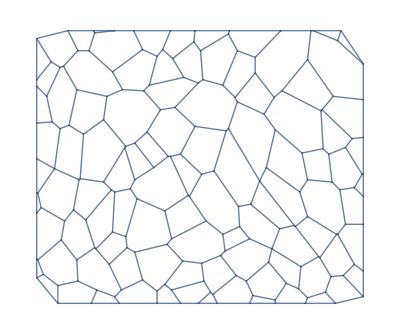

```mathematica
{segmentation,graphimage,cellToVerticesOrig}=getImageAttributes[image,False,True];
Echo@Graph[graphimage,ImageSize-> Tiny];
```

```mathematica
{ptsToIndAssoc,indToPtsAssoc,vertexToEdge}=getGraphAttributes[-Graphics-,image];
```

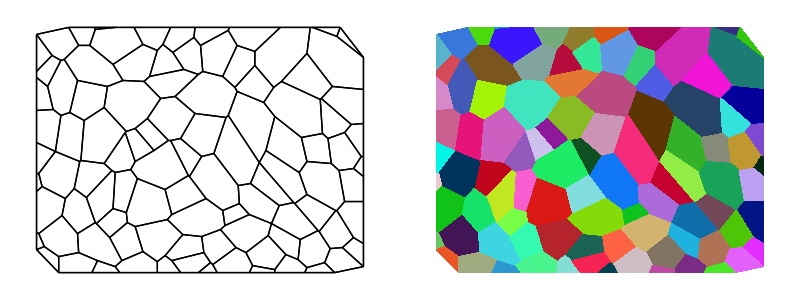

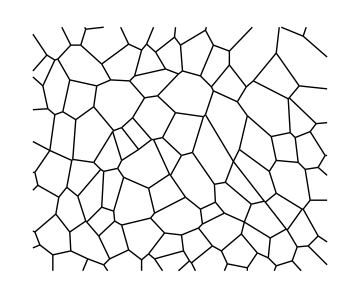

Tension coefficients computed: ☑

counts of zero coefficients Tx: 5

counts of zero coefficients Ty: 9

Tx coefficients stats: <|3→138,4→3,2→5|>

Ty coefficients stats: <|3→134,2→9,4→3|>

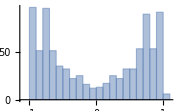
Tension coefficients dist: -Graphics-

Pressure coefficients computed: ☑

Pressure coefficients zero: 11

Px coefficients stats: <|3→135,4→3,2→8|>

Py coefficients stats: <|3→140,2→3,4→3|>

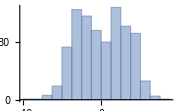
pressure coefficients dist: -Graphics-

maximum likelihood estimator

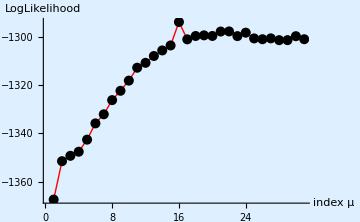

optimized value of μ: 1.

Tension map:

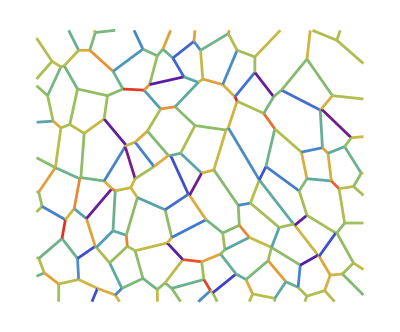

Pressure map:

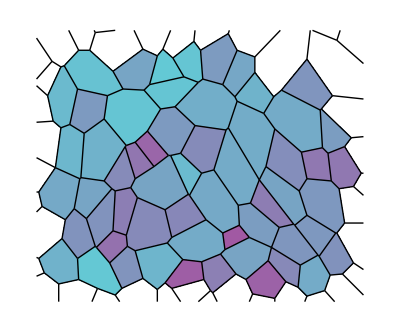

local stress tensor map:

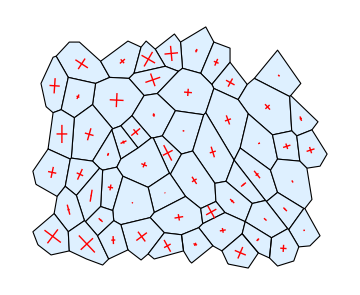

```mathematica
forceInference[image,cellToVerticesOrig,indToPtsAssoc,ptsToIndAssoc,segmentation,vertexToEdge,False,300]
```

global stress tensor map:

-Graphics-

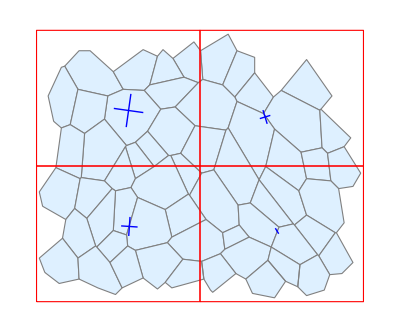

```mathematica
Print["global stress tensor map:"];
globalStressTensorMap[image,{2,2},$cells,$edgeAssoc,$pvals,$tensionAssoc,1000]
```

#### example 3

```mathematica
image=Binarize@Import@"D:\\LocalData\\hashmial\\scripts\\Force-Inference-master\\Force-Inference-master\\for ReadMe\\image.tif";
```

border exists, segmenting with watershed components

-Graphics-

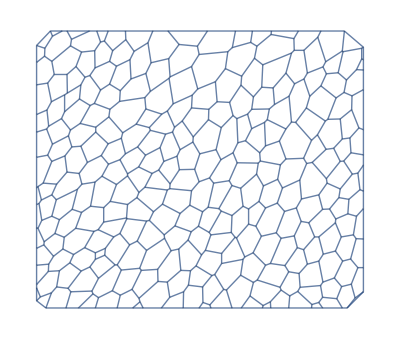

```mathematica
{segmentation,graphimage,cellToVerticesOrig}=getImageAttributes[image,False,True];
Echo@Graph[graphimage,ImageSize-> Tiny];
```

```mathematica
{ptsToIndAssoc,indToPtsAssoc,vertexToEdge}=getGraphAttributes[-Graphics-,image];
```

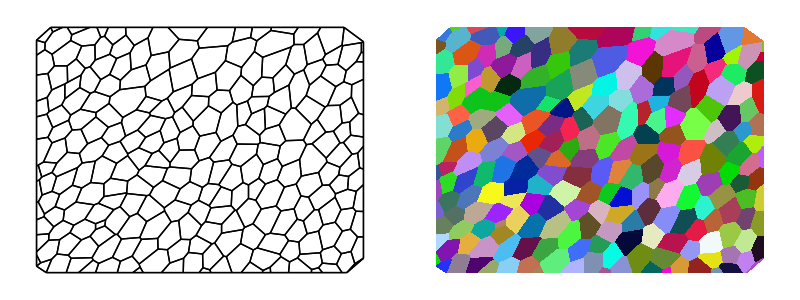

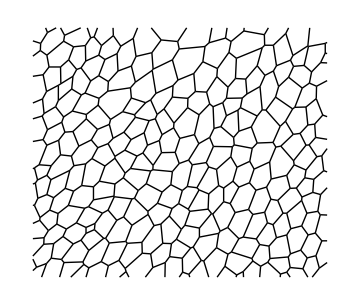

Tension coefficients computed: ☑

counts of zero coefficients Tx: 16

counts of zero coefficients Ty: 9

Tx coefficients stats: <|3→382,2→16|>

Ty coefficients stats: <|3→389,2→9|>

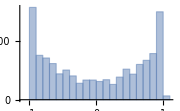
Tension coefficients dist: -Graphics-

Pressure coefficients computed: ☑

Pressure coefficients zero: 15

Px coefficients stats: <|3→393,2→5|>

Py coefficients stats: <|3→388,2→10|>

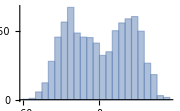
pressure coefficients dist: -Graphics-

maximum likelihood estimator

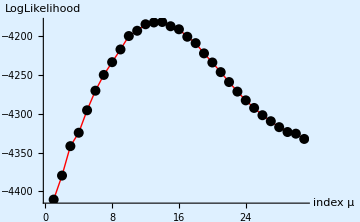

optimized value of μ: 0.630957

Tension map:

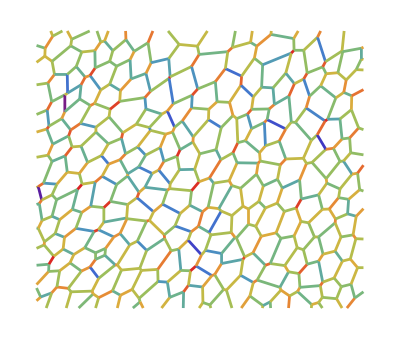

Pressure map:

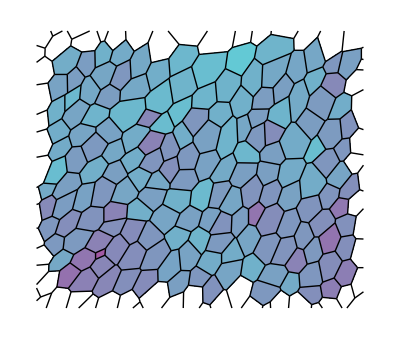

local stress tensor map:

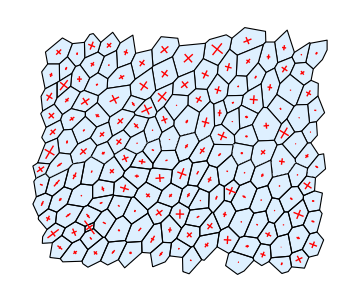

```mathematica
forceInference[image,cellToVerticesOrig,indToPtsAssoc,ptsToIndAssoc,segmentation,vertexToEdge,False,2000]
```

global stress tensor map:

-Graphics-

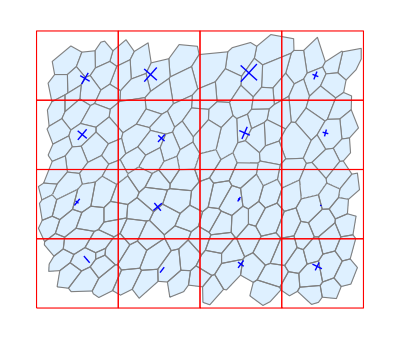

```mathematica
Print["global stress tensor map:"];
globalStressTensorMap[image,{4,4},$cells,$edgeAssoc,$pvals,$tensionAssoc,5000]
```

#### example 4

```mathematica
image=testimg[[1]];
```

-Graphics-

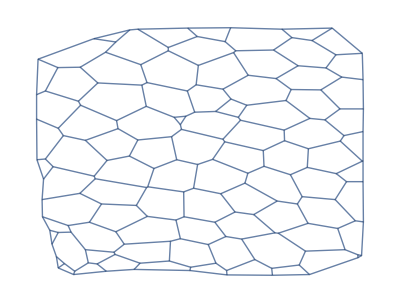

```mathematica
{segmentation,graphimage,cellToVerticesOrig}=getImageAttributes[image,True,True];
Echo@Graph[graphimage,ImageSize-> Tiny];
```

```mathematica
{ptsToIndAssoc,indToPtsAssoc,vertexToEdge}=getGraphAttributes[-Graphics-,image];
```

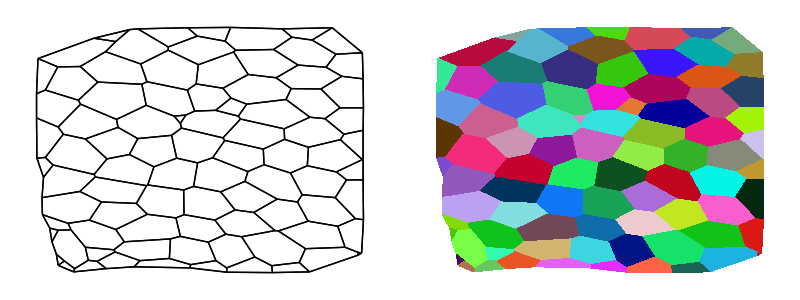

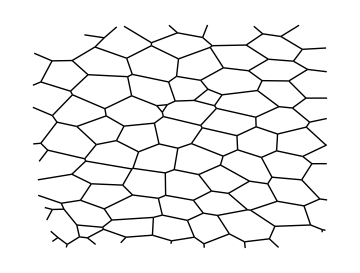

Tension coefficients computed: ☑

counts of zero coefficients Tx: 3

counts of zero coefficients Ty: 3

Tx coefficients stats: <|3→129,2→3|>

Ty coefficients stats: <|3→129,2→3|>

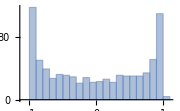
Tension coefficients dist: -Graphics-

Pressure coefficients computed: ☑

Pressure coefficients zero: 0

Px coefficients stats: <|3→132|>

Py coefficients stats: <|3→132|>

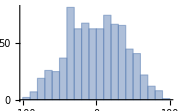
pressure coefficients dist: -Graphics-

maximum likelihood estimator

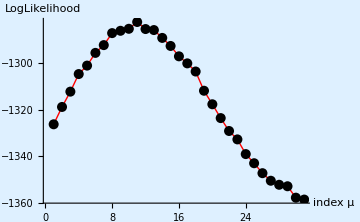

optimized value of μ: 0.316228

Tension map:

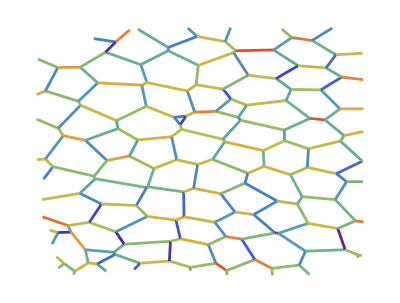

Pressure map:

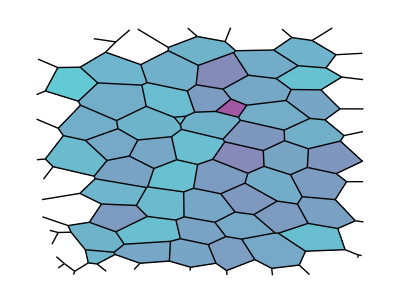

local stress tensor map:

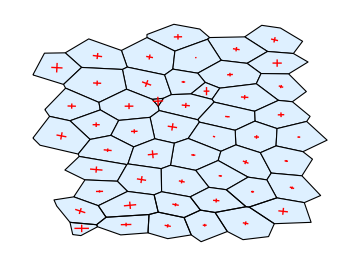

```mathematica
forceInference[image,cellToVerticesOrig,indToPtsAssoc,ptsToIndAssoc,segmentation,vertexToEdge,True,2000]
```

global stress tensor map:

-Graphics-

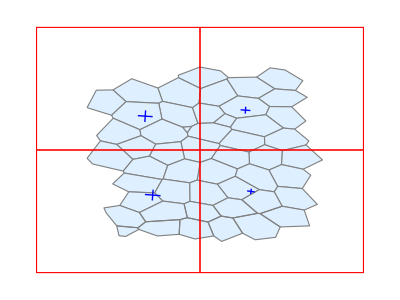

```mathematica
Print["global stress tensor map:"];
globalStressTensorMap[image,{2,2},$cells,$edgeAssoc,$pvals,$tensionAssoc,5000]
```